# Part 1.关于素数的一些探讨（3）

```mathematica
n=1;a=Table[Abs[Det[Table[Prime[i (n+1)+j+l],{i,0,n},{j,0,n}]]],{l,3,20000}];Min[a]
```

12

#### 进一步观察发现用a + b x log[x]拟合效果更好，而且分立的曲线其x log[x]前的系数确实呈线性关系

466.465+2.26912 x Log[x]

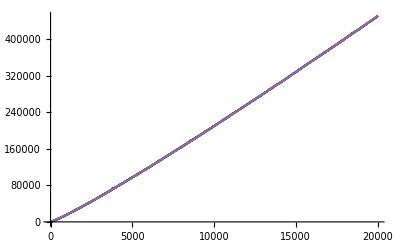

```mathematica
aaa=Select[Range[1,Length[a]],250+2# Log[#]<a[[#]]<500+3# Log[#]&];

aa=Union[Table[If[MemberQ[aaa,i],{i,a[[i]]},{1,1}],{i,1,Length[a]}]];
parabola=Fit[aa,{1,x Log[x]},x]
Show[ListPlot[aa, PlotStyle->Red], Plot[{parabola}, {x, 0, 20000}]]
```

947.866+4.53801 x Log[x]

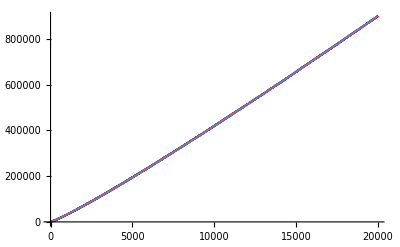

```mathematica
aaa=Select[Range[1,Length[a]],600+4# Log[#]<a[[#]]<1000+5# Log[#]&];

aa=Union[Table[If[MemberQ[aaa,i],{i,a[[i]]},{1,1}],{i,1,Length[a]}]];
parabola=Fit[aa,{x Log[x],1},x]
Show[ListPlot[aa, PlotStyle->Red], Plot[{parabola}, {x, 0, 20000}]]
```

1433.53+6.80717 x Log[x]

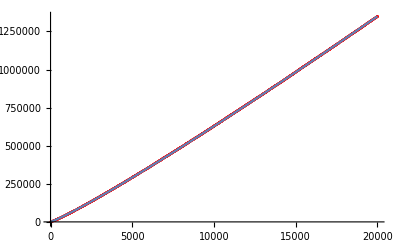

```mathematica
aaa=Select[Range[1,Length[a]],1000+6# Log[#]<a[[#]]<1500+7# Log[#]&];

aa=Union[Table[If[MemberQ[aaa,i],{i,a[[i]]},{1,1}],{i,1,Length[a]}]];
parabola=Fit[aa,{1,x Log[x]},x]
Show[ListPlot[aa, PlotStyle->Red], Plot[{parabola}, {x, 0, 20000}]]
```

### 而事实上，这一分立性是 很好解释的，而且其与x log[x]线性相关也是可以解释的 设P_(i+1)=P_i+a,P_(i+2)=P_i+a+b,P_(i+3)=P_i+a+b+c 则 D_i=|P_i*P_(i+3)-P_(i+1)*P_(i+2)|=(c-a)P_i-a^2-ab 从而由c-a的分立性可以粗略得出D_i 的分立性。 并且由于每个分支都是差不多是(c-a)P_i，而P_i~i log[i],所以我们会观察到如上现象。

# Part 2.Sn的最高阶元

```mathematica
CalcuOrder[g_]:=Module[{count=1,n,stand,h},n=Length[g];stand=Range[n];h=g;While[Norm[h-stand,1]>0.5,h=h[[g]];count=count+1;];
count]
```

我们希望找出Sn中最高阶元的次数，而这其实等价于问题：
已知n,对正整数变量x1,x2...xn,以及t,求满足x1+x2+...+xt=n情况下，最小公倍数lcm(x1,x2,...,xt)的最大值
下面就两次并行地计算了前25个值，两次求解结果一致。

```mathematica
Parallelize[Table[{t,Max[Table[g=Ordering[RandomReal[1,t]];CalcuOrder[g],{20000}]]},{t,25}]]//Timing
```

{0.859375,{{1,1},{2,2},{3,3},{4,4},{5,6},{6,6},{7,12},{8,15},{9,20},{10,30},{11,30},{12,60},{13,60},{14,84},{15,105},{16,140},{17,210},{18,210},{19,420},{20,420},{21,420},{22,420},{23,840},{24,840},{25,1260}}}

```mathematica
AbsoluteTiming[Parallelize[Table[{t,Max[Table[g=Ordering[RandomReal[1,t]];CalcuOrder[g],{20000}]]},{t,25}]]]
```

{43.0936,{{1,1},{2,2},{3,3},{4,4},{5,6},{6,6},{7,12},{8,15},{9,20},{10,30},{11,30},{12,60},{13,60},{14,84},{15,105},{16,140},{17,210},{18,210},{19,420},{20,420},{21,420},{22,420},{23,840},{24,840},{25,1260}}}

```mathematica
a={{1,1},{2,2},{3,3},{4,4},{5,6},{6,6},{7,12},{8,15},{9,20},{10,30},{11,30},{12,60},{13,60},{14,84},{15,105},{16,140},{17,210},{18,210},{19,420},{20,420},{21,420},{22,420},{23,840},{24,840},{25,1260}}
```

{{1,1},{2,2},{3,3},{4,4},{5,6},{6,6},{7,12},{8,15},{9,20},{10,30},{11,30},{12,60},{13,60},{14,84},{15,105},{16,140},{17,210},{18,210},{19,420},{20,420},{21,420},{22,420},{23,840},{24,840},{25,1260}}

```mathematica
Grid[a]
```

1 | 1
2 | 2
3 | 3
4 | 4
5 | 6
6 | 6
7 | 12
8 | 15
9 | 20
10 | 30
11 | 30
12 | 60
13 | 60
14 | 84
15 | 105
16 | 140
17 | 210
18 | 210
19 | 420
20 | 420
21 | 420
22 | 420
23 | 840
24 | 840
25 | 1260

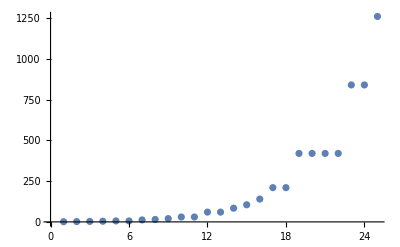

```mathematica
ListPlot[a]
```

### 问：如何从这些最高阶元看出原问题的解。 可以证明，取得最小公倍数最大值的时候，必定有每个xi都是素数或者1，于是我们只需把所得的结果分解因数，就可以得到取得最大值时的xi和t分别是多少了

```mathematica
Grid[Table[sum=0;factor=FactorInteger[a[[i]][[2]]],{i,Length[a]}]]
```

{1,1} |  |  | 
{2,1} |  |  | 
{3,1} |  |  | 
{2,2} |  |  | 
{2,1} | {3,1} |  | 
{2,1} | {3,1} |  | 
{2,2} | {3,1} |  | 
{3,1} | {5,1} |  | 
{2,2} | {5,1} |  | 
{2,1} | {3,1} | {5,1} | 
{2,1} | {3,1} | {5,1} | 
{2,2} | {3,1} | {5,1} | 
{2,2} | {3,1} | {5,1} | 
{2,2} | {3,1} | {7,1} | 
{3,1} | {5,1} | {7,1} | 
{2,2} | {5,1} | {7,1} | 
{2,1} | {3,1} | {5,1} | {7,1}
{2,1} | {3,1} | {5,1} | {7,1}
{2,2} | {3,1} | {5,1} | {7,1}
{2,2} | {3,1} | {5,1} | {7,1}
{2,2} | {3,1} | {5,1} | {7,1}
{2,2} | {3,1} | {5,1} | {7,1}
{2,3} | {3,1} | {5,1} | {7,1}
{2,3} | {3,1} | {5,1} | {7,1}
{2,2} | {3,2} | {5,1} | {7,1}

```mathematica
Table[sum=0;factor=FactorInteger[a[[i]][[2]]];j=1;Do[sum=sum+factor[[j]][[1]]^factor[[j]][[2]];j=j+1,{Length[factor]}];sum,{i,Length[a]}]
```

{1,2,3,4,5,5,7,8,9,10,10,12,12,14,15,16,17,17,19,19,19,19,23,23,25}

### 可以看出对一些n而言，取到最大值的时候，并不是恰好素数幂次的和就是n。但是有一些n而言，恰好和为n，我们称这样的n有素和分解。 比如5=2+3,7=2^2+3,那是不是素数就可以呢？ 但是11并不能恰好分解。 而且具有这一分解的数也没有可乘性，即4*5=20，但20并没有素和分解。。

```mathematica
AbsoluteTiming[Parallelize[Table[{t,Max[Table[g=Ordering[RandomReal[1,t]];CalcuOrder[g],{20000}]]},{t,26,30}]]]
```

{34.6856,{{26,1260},{27,1540},{28,2310},{29,2520},{30,4620}}}

```mathematica
AbsoluteTiming[Parallelize[Table[{t,Max[Table[g=Ordering[RandomReal[1,t]];CalcuOrder[g],{30000}]]},{t,26,40}]]]
```

{300.808,{{26,1260},{27,1540},{28,2310},{29,2520},{30,4620},{31,4620},{32,5460},{33,5460},{34,9240},{35,9240},{36,13860},{37,13860},{38,16380},{39,16380},{40,20020}}}

```mathematica
b={{26,1260},{27,1540},{28,2310},{29,2520},{30,4620},{31,4620},{32,5460},{33,5460},{34,9240},{35,9240},{36,13860},{37,13860},{38,16380},{39,16380},{40,20020}};
```

```mathematica
all=Join[a,b];primesum=Table[sum=0;factor=FactorInteger[all[[i]][[2]]];j=1;Do[sum=sum+factor[[j]][[1]]^factor[[j]][[2]];j=j+1,{Length[factor]}];sum,{i,Length[all]}]
```

{1,2,3,4,5,5,7,8,9,10,10,12,12,14,15,16,17,17,19,19,19,19,23,23,25,25,27,28,29,30,30,32,32,34,34,36,36,38,38,40}

```mathematica
Select[Range[Length[primesum]],#==primesum[[#]]&]
```

{1,2,3,4,5,7,8,9,10,12,14,15,16,17,19,23,25,27,28,29,30,32,34,36,38,40}

并没有很直观的性质。有待更深入地研究。